```mathematica
vars={c[x],{x}};Ω=Interval[{0,1}];gammaleft=MassImpermeableBoundaryValue[x==0,vars,<||>,<||>]
gammaright=MassTransferValue[x==1,vars,<|"MassTransferCoefficient"->1,"AmbientConcentration"->4|>,<||>];eqn=MassTransportPDEComponent[vars,<|"DiffusionCoefficient"->0.025,"Reaction"->(-2*c[x])|>]==gammaleft+gammaright cfun=NDSolveValue[{eqn},c,x∈Ω];Plot[cfun[x],x∈Ω,AxesLabel->{"x","c"}]
```

2

1

Interval[{0,2}]

NeumannValue[c[x] NeumannBoundaryUnitNormal[{x}].{0},x==0]

NeumannValue[2-c[x],x==2]

InterpolatingFunction[…]

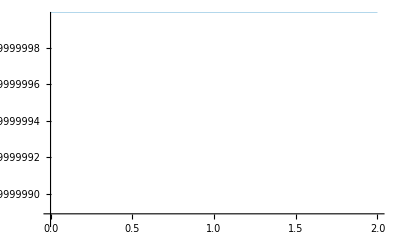

```mathematica
cExt=2 
P2ext=1 
Ω=Interval[{0,2}]
 vars={c[x],{x}};
gammaleft=MassImpermeableBoundaryValue[x==0,vars,pars,<||>]
gammaright=MassTransferValue[x==2,vars,<|"MassTransferCoefficient"->P2ext,"AmbientConcentration"->cExt|>,<||>]
cfun=NDSolveValue[{MassTransportPDEComponent[vars,<|"DiffusionCoefficient"->0.025,"Reaction"->(-2*c[x])|>]==gammaleft+gammaright},
c,{x}∈Ω
]
Plot[cfun[x],{x,0,2}]
```

```mathematica
cExt=2;
P2ext=1;
vars={c[x],{x}};
pars=<||>;
pars["DiffusionCoefficient"]=10^-4;

cfun=NDSolveValue[{MassTransportPDEComponent[vars,pars],MassImpermeableBoundaryValue[x==0,vars,pars,<||>],MassTransferValue[x==2,vars,<|"MassTransferCoefficient"->P2ext,"AmbientConcentration"->cExt|>,<||>]},c[x],{x}∈Interval[{0,2}]];

Plot[cfun[x],{x,0,2}]
```

NDSolveValue::deqn: Equation or list of equations expected instead of ( in the first argument {(,NeumannValue[c[x] NeumannBoundaryUnitNormal[{x}].{0},x==0],NeumannValue[2-c[x],x==2]}.

NDSolveValue::dsvar: True cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
Clear[x,y,t]


vars={c[x],{x}};
Ω=Interval[{0,2}];
cfun=NDSolveValue[{MassTransportPDEComponent[vars,<|"DiffusionCoefficient"->0.0001,"Reaction"->(-2 c[x])|>],MassImpermeableBoundaryValue[x==0,vars,<||>,<||>],MassTransferValue[x==2,vars,<|"MassTransferCoefficient"->1,"AmbientConcentration"->2|>,<||>]},c[x],{x}∈Ω];

Plot[cfun[x],{x,0,2},AxesLabel->{"x","c"}]
```

NDSolveValue::deqn: Equation or list of equations expected instead of ( in the first argument {(,NeumannValue[c[x] NeumannBoundaryUnitNormal[{x}].{0},x==0],NeumannValue[2-c[x],x==2]}.

NDSolveValue::dsvar: True cannot be used as a variable.

General::stop: Further output of NDSolveValue::dsvar will be suppressed during this calculation.

-Graphics-